```mathematica
f[x_]:=Exp[-x^2];
```

```mathematica
g[x_]=f'[x];
```

```mathematica
g[x]
```

-2 ⅇ^(-x^2) x

```mathematica
FullForm[h'[x]]
```

```mathematica
Derivative[1][f][x]
```

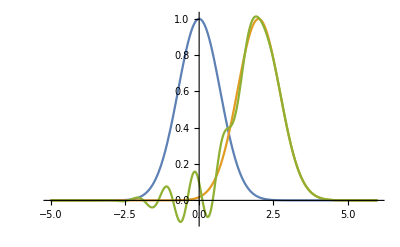

```mathematica
a=2;
Plot[{f[x],f[x-a],Sum[((-a)^n*Derivative[n][f][x])/(n!),{n,0,20}]},{x,-5,6},PlotRange->All]
```

```mathematica
f[x]+Sum[(-g[x])^i/(i!),{i,1,2}]
f[x]-1*g[x]+1/2*(1*g[x])^2
```

ⅇ^(-x^2)+2 ⅇ^(-x^2) x+2 ⅇ^(-2 x^2) x^2

ⅇ^(-x^2)+2 ⅇ^(-x^2) x+2 ⅇ^(-2 x^2) x^2

```mathematica
f[x]-1*g[x]
```

ⅇ^(-x^2)+2 ⅇ^(-x^2) x

```mathematica
Series[Exp[x],{x,0,10}]
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+x^9/362880+x^10/3628800+O[x]^11